```mathematica
(* This is necessary for removing previously defined variables *)
ClearAll["Global`*"]
```

## Misc Modules

```mathematica
stripList[lst_]:=Module[{lst2},
lst2 = List[];
Do[AppendTo[lst2,Last[lst[[ii]]]],{ii,Length[lst]}];
Return[lst2]]
```

```mathematica
a=List[{1},{2},{3}]
stripList[a]
```

{{1},{2},{3}}

{1,2,3}

```mathematica
(* Write Module to Count number of roots in a function *)
(* From https://www.physicsforums.com/threads/find-all-roots-of-an-interpolating-function-in-mathematica.612362/ *)
countZeros[ifun_,xmin_,xmax_,dx_] := Module[{zeros,numZeros},
zeros = Union[Table[x/.FindRoot[ifun[x]==0.,{x,xInit,xmin,xmax}],{xInit,xmin+dx,xmax-dx,dx}],SameTest->(Abs[#1-#2]<10^-4&)];
numZeros = Length[zeros];
Print[zeros];
If[Last[zeros]==xmax,If[ifun[xmax]≠0,numZeros=numZeros-1]];
If[First[zeros]==xmin,If[ifun[xmin]≠0,numZeros=numZeros-1]];
Return[numZeros]]
```

```mathematica
f[x_]:=x^4-x^2
countZeros[f,-2,2,0.1]
```

{-1.,-1.01172×10^-8,1.}

3

```mathematica
countAllZeros[ifun_,xmin_,xmax_,dx_,hardLim_]:=Module[{z,ztot,num,ii},
z=countZeros[ifun,xmin,xmax,dx];
Print["number of zeros for the function is ",z];
ztot=z;
If[z==0,num=0,num=1];
ii=1;
While[True,
f[x_]=D[ifun[x],{x,ii}];
If[f[x_]==0,Break[]];
z=countZeros[f,xmin,xmax,dx];
Print["number of zeros for ",ii,"th derivative is ",z];
ztot=ztot+z;
If[z==0,num++];
If[num≥2,Break[]];
If[ii≥hardLim,Break[]];
ii++];
Return[ztot]]
```

```mathematica
f[x_]:=x^4-x^2
countAllZeros[f,-10,10,0.1,1]
```

{-1.,-1.01172×10^-8,1.}

number of zeros for the function is 3

{-0.707107,-1.17155×10^-19,0.707107}

number of zeros for 1th derivative is 3

6

## Cosmology Calculation Modules

```mathematica
findZϵsr[v_,vp_,ϕsol_,nmin_,nmax_,dn_,hardLim_]:=Module[{ϵsr,f,z,num,ii,ztot},
ϵsr[x_]:=1/2*(vp[x]/v[x])^2;
f[n_]:=ϵsr[ϕ[n]]/.ϕsol;
Print[Plot[Evaluate[f[n]],{n,nmin,nmax},AxesLabel->{N,"ϵsr"},PlotRange->{-1,1}]];
z=countZeros[f,nmin,nmax,dn];
Print["number of zeros for ϵsr is ",z];
ztot=z;
If[z==0,num=0,num=1];
ii=1;
While[True,
f[n_]=D[ϵsr[ϕ[n]]/.ϕsol,{n,ii}];
Print[Plot[Evaluate[f[n]],{n,nmin,nmax},AxesLabel->{N,ii},PlotRange->{-1,1}]];
If[f[n_]==0,Break[]];
z=countZeros[f,nmin,nmax,dn];
Print["number of zeros for ",ii,"th derivative of ϵ is ",z];
ztot=ztot+z;
If[z==0,num++];
If[num≥2,Break[]];
If[ii≥hardLim,Break[]];
ii++];
Return[ztot]]
```

```mathematica
findZϵ[v_,ϕsol_,nmin_,nmax_,dn_,hardLim_]:=Module[{hsq,ϵ,f,z,num,ii,ztot},
hsq[n_]:=v[ϕ[n]]/(3-1/2*ϕ'[n]^2);
ϵ[n_] = Evaluate[3*ϕ'[n]^2/(ϕ'[n]^2+2*v[ϕ[n]]/hsq[n])];
f[n_] = ϵ[n]/.ϕsol;
Print[Plot[Evaluate[f[n]],{n,nmin,nmax},AxesLabel->{N,"ϵ"},PlotRange->{-1,1}]];
z=countZeros[f,nmin,nmax,dn];
Print["number of zeros for ϵ is ",z];
ztot=z;
If[z==0,num=0,num=1];
ii=1;
While[True,
f[n_]=D[ϵ[ϕ[n]],{n,ii}]/.ϕsol;
Print[Plot[Evaluate[f[n]],{n,nmin,nmax},AxesLabel->{N,ii},PlotRange->{-1,1}]];
If[f[n_]==0,Break[]];
z=countZeros[f,nmin,nmax,dn];
Print["number of zeros for ",ii,"th derivative of ϵ is ",z];
ztot=ztot+z;
If[z==0,num++];
If[num≥2,Break[]];
If[ii≥hardLim,Break[]];
ii++];
Return[ztot]]
```

```mathematica
findZη[v_,vpp_,ϕsol_,nmin_,nmax_,dn_,hardLim_]:=Module[{ηsr,f,z,num,ii,ztot},
ηsr[n_]:=vpp[ϕ[n]]/v[ϕ[n]];
f[n_]:=ηsr[ϕ[n]]/.ϕsol;
Print[Plot[Evaluate[f[n]],{n,nmin,nmax},AxesLabel->{N,"ηsr"},PlotRange->{-1,1}]];
z=countZeros[f,nmin,nmax,dn];
Print["number of zeros for ηsr is ",z];
ztot=z;
If[z==0,num=0,num=1];
ii=1;
While[True,
f[n_]=D[ηsr[ϕ[n]]/.ϕsol,{n,ii}];
Print[Plot[Evaluate[f[n]],{n,nmin,nmax},AxesLabel->{N,ii},PlotRange->{-1,1}]];
If[f[n_]==0,Break[]];
z=countZeros[f,nmin,nmax,dn];
Print["number of zeros for ",ii,"th derivative of η is ",z];
ztot=ztot+z;
If[z==0,num++];
If[num≥2,Break[]];
If[ii≥hardLim,Break[]];
ii++];
Return[ztot]]
```

```mathematica
findH[v_]:=Module[{h,hsq},
h[n_]:= Simplify[√(v[ϕ[n]]/(3-1/2*ϕ'[n]^2))];
hsq[n_]:=v[ϕ[n]]/(3-1/2*ϕ'[n]^2);
Return[{h,hsq}]]
```

### Find Initial Conditions for 1st Integration

```mathematica
chooseϕ0Manual[ϕ0list_]:=Module[{ϕ0index,ϕ0},
ϕ0index = Input["Enter the index for the ϕ0 you want to use: \n(Counting starts at 1)"];
ϕ0 = ϕ0list[[ϕ0index]]; 
Return[ϕ0]]
```

```mathematica
chooseϕ0Left[ϕ0list_,v_]:=Module[{ϕ0listpos,ϕ0,vacuumArray},
ϕ0listpos=Select[ϕ0list,#>0&];
(* vacuum = First[Select[ϕ0listpos,v[#]<10^-6&]];
ϕ0 = Max[Select[ϕ0listpos,#<vacuum&]]; *)
If[ϕ0listpos=={},
vacuumArray =Select[ϕ0list,v[#]<10^-6&];
Print["vacuumArray = ",vacuumArray];
If[vacuumArray=={},ϕ0=Min[ϕ0list],
ϕ0 = Min[Select[ϕ0list,#<First[vacuumArray]&]]];,
(*else*)
vacuumArray =Select[ϕ0listpos,v[#]<10^-6&];
Print["vacuumArray = ",vacuumArray];
If[vacuumArray=={},ϕ0=Min[ϕ0listpos],
ϕ0 = Max[Select[ϕ0listpos,#<First[vacuumArray]&]]];
];
Return[ϕ0]]
```

```mathematica
chooseϕ0Right[ϕ0list_,v_]:=Module[{ϕ0listpos,ϕ0,vacuumArray},
ϕ0listpos=Select[ϕ0list,#≥0&];
If[ϕ0listpos=={},
vacuumArray =Select[ϕ0list,v[#]<10^-6&];
Print["vacuumArray = ",vacuumArray];
If[vacuumArray=={},ϕ0=Max[ϕ0list],
ϕ0 = Max[Select[ϕ0list,#>First[vacuumArray]&]]];,
(* else *)
vacuumArray =Select[ϕ0listpos,v[#]<10^-6&];
Print["vacuumArray = ",vacuumArray];
If[vacuumArray=={},ϕ0=Max[ϕ0listpos],
ϕ0 = Min[Select[ϕ0listpos,#>First[vacuumArray]&]]];
];
Return[ϕ0]]
```

```mathematica
guessϕiLeft[v_,vpp_,ni_,ϕ0_]:=Module[{guesses,ϕiguess},
guesses = t/.NSolve[ni==v[t]/vpp[t],t];
Print["guesses = ",guesses];
ϕiguess=Min[Select[guesses,#>0&&#<ϕ0&]];
Return[ϕiguess]]
```

```mathematica
guessϕiRight[v_,vpp_,ni_,ϕ0_]:=Module[{guesses,ϕiguess},
guesses = t/.NSolve[ni==v[t]/vpp[t],t];
Print["guesses = ",guesses];
ϕiguess=Min[Select[guesses,#>0&&#>ϕ0&]];
Return[ϕiguess]]
```

```mathematica
findICsr[v_,vp_,vpp_,ni_,plots_,prints_,left_]:=Module[{ϕ0list,ϕ0index,ϕ0,f,ϕiguess,ϕi1s,ϕi1,ϕpi1,vplt,ϕ0plt,ϕiplt,ϕi1sol},
vplt = Plot[v[x],{x,-10,10},AxesLabel->{"ϕ","V"}];
(* Solve for where ϵ=1 and hence N=0 *)
ϕ0list = Normal[NSolve[vp[x]==√2*v[x],x,Reals]]/.C[1]->0;
ϕ0list = Values[stripList[Union[ϕ0list,Normal[NSolve[vp[x]==-√2*v[x],x,Reals]]/.C[1]->0]]];
Print["ϕ0list = ",ϕ0list];
If[plots,ϕ0plt = ListPlot[Transpose[{ϕ0list,v[ϕ0list]}]]; (* Transpose is Zip!! *)
Print[Show[vplt,ϕ0plt]]];
If[left,ϕ0 = chooseϕ0Left[ϕ0list,v],ϕ0 = chooseϕ0Right[ϕ0list,v]];
If[prints,Print["ϕ0 = ",ϕ0]];
(* Integrate up the hill to find the value of ϕ at ni *)
f[t_] = Integrate[v[x]/vp[x],{x,ϕ0,t}];
If[prints,Print["f[t] = ",f[t]]]; 
If[prints,Print["f[0.01] = ",f[0.01]]]; 
(* Print["N slow roll = ",v[t]/vpp[t]/.t->0.1]; *)
(*If[plots,Print[LogLogPlot[{Legended[Evaluate[f[t]],"Integration"],Legended[v[t]/vpp[t],"Slow Roll"]},{t,10^-5,10},AxesLabel->{"ϕ","N"}]]]; *)
(*ϕi1= t/.Last[NSolve[ni==f[t],t]];*)
(* ϕiguess = Input["Enter a guess for ϕi1"]; *)
(* ϕiguess = guessϕiLeft[v,vpp,ni,ϕ0];
If[prints,Print["ϕiguess = ",ϕiguess]];
ϕi1= t/.Last[FindRoot[ni-f[t],{t,ϕiguess}]]; *)
ϕi1sol = NSolve[ni==f[t]&&t≥0 && t≤ϕ0,t];
If[prints,Print["NSolve ni==f[t] returns: ",ϕi1sol]];
If[left,ϕi1s = t/.ϕi1sol,
ϕi1s = t/.NSolve[ni==f[t]&&t≥0 && t≥ϕ0,t]];
Print["ϕi1s = ",ϕi1s];
ϕi1 = Last[ϕi1s];
ϕpi1 = vp[ϕi1]/v[ϕi1] ;
If[plots,ϕiplt = ListPlot[{{ϕi1,v[ϕi1]},{ϕ0,v[ϕ0]}}];
Print[Show[vplt,ϕiplt]]];
Return[{ϕi1,ϕpi1}]]
```

### Find Initial Conditions for 2nd Integration

```mathematica
findICshifted[v_,ϕsol1_,prints_,plots_]:=Module[{ϵ1,n1,ϕi2,ϕpi2},
(* Find ϵ1 *)
ϵ1=findϵ[v,ϕsol1];
If[prints,Print["At n = 0",", ϵ1 = ",Evaluate[ϵ1[n]/.n->0]]];
If[plots,Print[Plot[Evaluate[ϵ1[n]],{n,nf,ni},AxesLabel->{N,"ϵ1"},PlotRange->{{nf,-nf},{0,2}},GridLines->{{-1,-1.2},{1}}]]];
(* Solve for where ϵ1[n]==1 *)
n1 = Evaluate[n/.First[FindRoot[ϵ1[n]-1,{n,n1guess}]]];
If[prints,Print["At n1 = ",n1,", ϵ1 = ",Evaluate[ϵ1[n]/.n->n1]]];
(* Find the new initial conditions *)
ϕi2 = Re[ϕ[ni2+n1]/.ϕsol1];
If[prints,Print["ϕi2 = ",ϕi2]];
ϕpi2 = Re[D[ϕ[n],n]/.ϕsol1/.n->(ni2+n1)];
If[prints,Print["ϕpi2 = ",ϕpi2]];
Return[{ϕi2,ϕpi2}]]
```

```mathematica
solveKG[hsq_,vp_,ni_,nf_,ϕi1_,ϕpi1_,plots_]:=Module[{ϕsol1},
ϕsol1 = Last@Last@NDSolve[{2*hsq[n]*ϕ''[n]+hsq[n]*(ϕ'[n])^3-6*hsq[n]*ϕ'[n]+2*vp[ϕ[n]]==0,ϕ[ni]==ϕi1,ϕ'[ni]==ϕpi1},ϕ,{n,ni,nf},InterpolationOrder->All];
If[plots,Print[Plot[Evaluate[ϕ[n]/.ϕsol1],{n,nf,ni},AxesLabel->{N,"ϕsol"},GridLines->{{-1,-1.2},{1}}]]];
Return[ϕsol1]]
```

### Find Epsilon

```mathematica
findϵ[v_,ϕsol_]:=Module[{ϕp,hsq,ϵ,η},
ϕp[n_] = D[ϕ[n],n]/.ϕsol;
hsq[n_]:=v[ϕ[n]]/(3-1/2*ϕp[n]^2)/.ϕsol;
ϵ[n_] = Evaluate[3*ϕp[n]^2/(ϕp[n]^2+2*v[ϕ[n]]/hsq[n])/.ϕsol];
(* above took out a Re[] just inside the Evaluate[] *)
(* η[n_] = D[ϵ[n],n]; *)
Return[ϵ]]
```

```mathematica
findϕsol[v_,vp_,vpp_,ni_,nf_,ni2_,nf2_,n1guess_,plots_,prints_,left_]:=Module[{h,hsq,ϕi1,ϕpi1,ϕsol1,ϕi2,ϕpi2,ϕsol2},
(* Define the hubble parameter *)
{h,hsq}=findH[v];
(* Find the slow roll initial conditions *)
{ϕi1,ϕpi1}=findICsr[v,vp,vpp,ni,plots,prints,left];
(* Solve the Klein-Gordon equation for ϕ1[n] *)
ϕsol1 = solveKG[hsq,vp,ni,nf,ϕi1,ϕpi1,plots];
(* Find the new initial conditions and re-solve the KG equation *)
{ϕi2,ϕpi2}=findICshifted[v,ϕsol1,prints,plots];
ϕsol2 = solveKG[hsq,vp,ni2,nf2,ϕi2,ϕpi2,plots];
(* Note: before I had it integrating from nf2 to ni2 *)
If[prints,Print["ϕsol2[60] = ",ϕ[60]/.ϕsol2]];
Return[ϕsol2]]
```

```mathematica
findNsR[v_,vp_,ϕsol2_,ni2_,nf2_,plots_,prints_] := Module[{ϕ2p,h2sq,ϵ2,ns,r,ϵsr,ϵsrL,ηsr,ηsrL,Zϵ,Zη },
(* Find ϵ2 *)
ϵ2 = findϵ[v,ϕsol2];
If[prints,Print["At n = 0",", ϵ1 = ",Evaluate[ϵ2[n]/.n->0]]];
If[plots,Print[Plot[Evaluate[ϵ2[n]],{n,nf2,ni2},AxesLabel->{N,"ϵ2"},PlotRange->{{nf2,ni2},{0,1}}]]];
(* Find the spectral tilt: ns[n] *)
ns[n_] := 1-2*ϵ2[n]+D[Log[ϵ2[n]],n];
If[prints,Print["ns[60] = ",ns[n]/.{n->60}]];
r[n_] := 16*ϵ2[n];
If[prints,Print["r[60] = ",r[n]/.{n->60}]];
If[plots,Print[Plot[Evaluate[ns[n]],{n,nf2,ni2},AxesLabel->{N,"ns"}]]];
Return[{ns[n],r[n],ϵ2}]];
```

```mathematica
findSRparams[v_,vp_,vpp_,ϕsol2_,ni2_,nf2_,prints_,plots_]:=Module[{ϵsr,ϵsrL,ηsr,ηsrL},
(* Find slow roll params ϵsr and ηsr *)
ϵsr[n_]:=1/2*(vp[ϕ[n]]/v[ϕ[n]])^2/.ϕsol2;
ϵsrL[n_]:=1/2*D[Log[v[ϕ[n]]],n]/.ϕsol2;
If[prints,Print["ϵsr[0] = ",ϵsr[n]/.{n->0}]];
If[prints,Print["ϵsr[60] = ",ϵsr[n]/.{n->60}]];
If[prints,Print["ϵsrL[0] = ",ϵsrL[n]/.{n->0}]];
If[prints,Print["ϵsrL[60] = ",ϵsrL[n]/.{n->60}]];
If[plots,Print[Plot[Evaluate[1/2*(vp[x]/v[x])^2],{x,0,30},AxesLabel->{"ϕ","ϵ[ϕ]"},PlotRange->{0,10}]]];
If[plots,Print[Plot[{Legended[Evaluate[ϵsr[n]],"ϵsr"],Legended[ϵ2[n],"ϵ2"],Legended[Evaluate[ϵsrL[n]],"ϵsrL"]},{n,nf2,ni2},AxesLabel->{N,"ϵsr"},PlotRange->{{nf2,ni2},{0,3}}]]];
ηsr[n_]:=vpp[ϕ[n]]/v[ϕ[n]]/.ϕsol2;
ηsrL[n_]:=1/2*D[Log[vp[ϕ[n]^2]],n]/.ϕsol2;If[prints,Print["ηsr[0] = ",ηsr[n]/.{n->0}]];
If[prints,Print["ηsr[60] = ",ηsr[n]/.{n->60}]];
If[plots,Print[Plot[Evaluate[vpp[x]/v[x]],{x,0,30},AxesLabel->{"ϕ","η[ϕ]"},PlotRange->{0,10}]]];
If[plots,Print[Plot[{Legended[Evaluate[ηsr[n]],"ηsr"],Legended[Evaluate[ηsrL[n]],"ηsrL"]},{n,nf2,ni2},AxesLabel->{N,"ηsr"},PlotRange->{{nf2,ni2},{0,3}}]]];
Return[{ϵsr,ηsr,ηsrL}]]
```

## Define Potential & Solve for Cosmological Parameters

#### (run the next two cells to get desired output!)

```mathematica
(* Define an inflationary potential *)
left = False;
(* v[x_] := x^(2/3); *) (* works *)
(* v[x_]:=(0.01)*((x^2-(10)^2)^2 ); *) (* works *)
(* v[x_]:=1/2*(1+Cos[x/8.8388]); *) (* broke *)
(* v[x_]:=(0.5)*(1+Cos[x/4.0]); *) (* broke 8.8388 *)
(* v[x_]:=(0.01)*(1-(1/x)^2); *) (* D-brane *)
v[x_]:=(0.01)*(1-Exp[-0.01*x]);
(*v[x_]:=(0.1)*(1-Exp[-(0.1)*x]);*) (* works *)
(*v[x_]:=(0.1)*(1+10*Exp[-2*x/√6])^-2;*) (* works *) (*v[x_]:=(0.1)*(1+Exp[-2*x/√6])^-2;*) (* works *) (* Shaposhnikov model *)
(* v[x_]:=(0.1)*(1-Exp[-√(2/3)*x])^2; *) (* Starobinsky model *)
(* v[x_]:=1-2/(5)^2*x^2;  *)
(* v[x_]:=x^4; *) (* works *)
(* v[x_] := 1-1/2*(0.7)^2*x^2+(44^2/0.7)*x^4; *)
(* Plot[v[x],{x,-10,10}] *)
vp[x_]=v'[x];
vpp[x_] = v''[x];
ni = 60; (* initial value f n for integration *)
nf = -1.8; (* final value of n for integration *)
ni2 = 60;
nf2 = 0;
n1guess = -1;
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

ϕ0list = {-0.709619,0.704619}

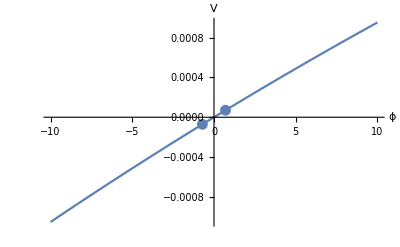

vacuumArray = {}

ϕ0 = 0.704619

f[t] = -10000.2+10000. ⅇ^(0.01 t)-100. t

f[0.01] = -0.248778

NSolve ni==f[t] returns: {}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve :: ratnz will be suppressed during this calculation.

ϕi1s = {10.7799}

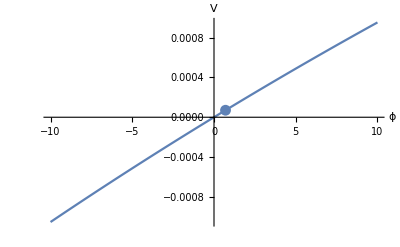

NDSolve::ndsz: At n == -1.40465, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {-1.79874} lies outside the range of data in the interpolating function. Extrapolation will be used.

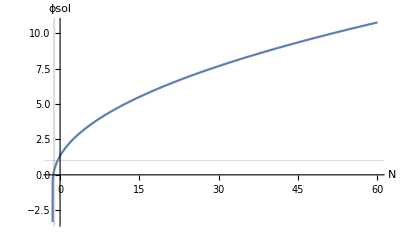

At n = 0, ϵ1 = 0.210695

InterpolatingFunction::dmval: Input value {-1.79874} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

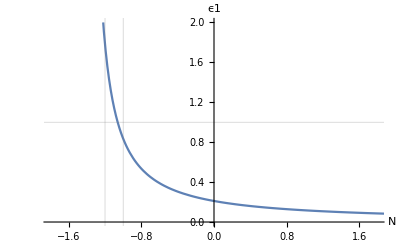

At n1 = -1.06066, ϵ1 = 1.

ϕi2 = 10.6865

ϕpi2 = 0.0884193

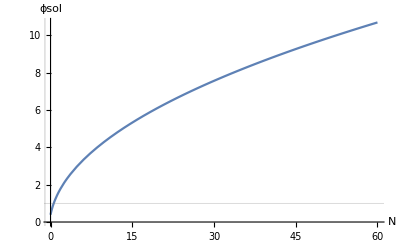

ϕsol2[60] = 10.6865

At n = 0, ϵ1 = 1.00009

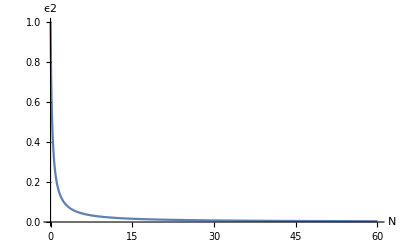

ns[60] = 0.975531

r[60] = 0.0625437

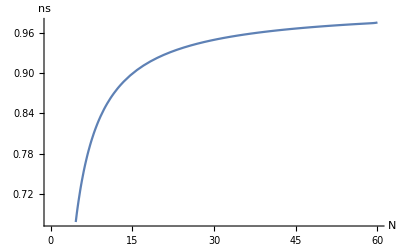

```mathematica
ϕsol2=findϕsol[v,vp,vpp,ni,nf,ni2,nf2,n1guess,True,True,left];
{ns,r,ϵ2} = findNsR[v,vp,ϕsol2,ni2,nf2,True,True];
```

## Replicate Planck Plot

#### Hilltop Models: V=λ(ϕ^2 - σ^2)^2

```mathematica
σList = {5,7,10,12,15,17,20,22,25,26,30,40,50,60,70,80,100};
ns60List={};ns50List={};r60List={};r50List={};
Do[
Print["σ = ",σ];
v[x_]:=(0.01)*((x^2-(σ)^2)^2 );
vp[x_]=v'[x];
vpp[x_] = v''[x];

ni = 60; (* initial value f n for integration *)
nf = -1.8; (* final value of n for integration *)
ni2 = 60;
nf2 = 0;
n1guess = -1;

ϕsol2=findϕsol[v,vp,vpp,ni,nf,ni2,nf2,n1guess,False,False, True];
{ns,r,ϵ2} = findNsR[v,vp,ϕsol2,ni2,nf2,False,False]; 
AppendTo[ns60List,ns/.{n->60}];
AppendTo[ns50List,ns/.{n->50}];
AppendTo[r60List,r/.{n->60}];
AppendTo[r50List,r/.{n->50}];
,{σ,σList}]
```

σ = 5

ϕ0list = {-6.61037,-5.,-5.,-3.78194,3.78194,5.,5.,6.61037}

vacuumArray = {5.,5.}

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

ϕi1s = {0.000192421}

InterpolatingFunction::dmval: Input value {-20.2786} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-2.92786} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-4.72026} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

σ = 7

ϕ0list = {-8.55564,-7.,-7.,-5.72721,5.72721,7.,7.,8.55564}

vacuumArray = {7.,7.}

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

ϕi1s = {0.0305795}

σ = 10

ϕ0list = {-11.5137,-10.,-10.,-8.68529,8.68529,10.,10.,11.5137}

vacuumArray = {10.,10.}

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of NSolve :: ratnz will be suppressed during this calculation.

ϕi1s = {0.541141}

σ = 12

ϕ0list = {-13.4973,-12.,-12.,-10.6688,10.6688,12.,12.,13.4973}

vacuumArray = {12.,12.}

ϕi1s = {1.36604}

σ = 15

ϕ0list = {-16.4807,-15.,-13.6523,13.6523,15.,16.4807}

vacuumArray = {15.}

ϕi1s = {3.17548}

σ = 17

ϕ0list = {-18.4729,-17.,-17.,-15.6445,15.6445,17.,17.,18.4729}

vacuumArray = {17.,17.}

ϕi1s = {4.63379}

σ = 20

ϕ0list = {-21.4642,-20.,-20.,-18.6357,18.6357,20.,20.,21.4642}

vacuumArray = {20.,20.}

ϕi1s = {7.05055}

σ = 22

ϕ0list = {-23.4596,-22.,-22.,-20.6312,20.6312,22.,22.,23.4596}

vacuumArray = {22.,22.}

ϕi1s = {8.7631}

σ = 25

ϕ0list = {-26.4542,-25.,-25.,-23.6258,23.6258,25.,25.,26.4542}

vacuumArray = {25.,25.}

ϕi1s = {11.431}

σ = 26

ϕ0list = {-27.4526,-26.,-26.,-24.6242,24.6242,26.,26.,27.4526}

vacuumArray = {26.,26.}

ϕi1s = {12.34}

σ = 30

ϕ0list = {-31.4475,-30.,-30.,-28.6191,28.6191,30.,30.,31.4475}

vacuumArray = {30.,30.}

ϕi1s = {16.0451}

σ = 40

ϕ0list = {-41.4392,-40.,-40.,-38.6108,38.6108,40.,40.,41.4392}

vacuumArray = {40.,40.}

ϕi1s = {25.5942}

σ = 50

ϕ0list = {-51.4342,-50.,-50.,-48.6058,48.6058,50.,50.,51.4342}

vacuumArray = {50.,50.}

ϕi1s = {35.3404}

σ = 60

ϕ0list = {-61.4309,-60.,-60.,-58.6025,58.6025,60.,60.,61.4309}

vacuumArray = {60.,60.}

ϕi1s = {45.178}

σ = 70

ϕ0list = {-71.4285,-70.,-70.,-68.6001,68.6001,70.,70.,71.4285}

vacuumArray = {70.,70.}

ϕi1s = {55.0653}

σ = 80

ϕ0list = {-81.4267,-80.,-80.,-78.5983,78.5983,80.,80.,81.4267}

vacuumArray = {80.,80.}

ϕi1s = {64.9825}

σ = 100

ϕ0list = {-101.424,-100.,-100.,-98.5958,98.5958,100.,100.,101.424}

vacuumArray = {100.,100.}

ϕi1s = {84.8692}

{0.695701,0.841048,0.92033,0.941809,0.956532,0.96113,0.964736,0.966033,0.967164,0.967408,0.968017,0.968443,0.968441,0.968357,0.968263,0.968176,0.968034}

{2.18433×10^-8,0.0000681516,0.00417541,0.0125927,0.0290602,0.0396391,0.0531957,0.0606572,0.0698636,0.0724894,0.0812703,0.095403,0.103662,0.109035,0.112797,0.115575,0.119397}

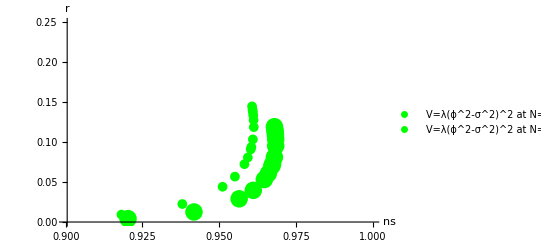

```mathematica
ns60List
r60List
nsmin = 0.9; nsmax = 1; rmin = 0; rmax = 0.25;
p1 = ListPlot[Legended[Transpose[{ns60List,r60List}],"V=λ(ϕ^2-σ^2)^2 at N=60"],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotMarkers->{●,18},PlotStyle->Green];
p2 = ListPlot[Legended[Transpose[{ns50List,r50List}],"V=λ(ϕ^2-σ^2)^2 at N=60"],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotMarkers->{●,10},PlotStyle->Green,PlotLegends->PointLegend[Automatic,{"Hilltop at N=50"}]];

Show[p1,p2]
```

### Hilltop Models: V=λ(1 - (ϕ/μ)^2 )

```mathematica
μList = {5,7,10,12,15,17,20,22,25,30,40,50,60,70,80,100};
ns60Listμ={};ns50Listμ={};r60Listμ={};r50Listμ={};
Do[
Print["μ = ",μ];
v[x_]:=(0.01)*(1-(x/μ)^2);
vp[x_]=v'[x];
vpp[x_] = v''[x];

ni = 60; (* initial value f n for integration *)
nf = -1.8; (* final value of n for integration *)
ni2 = 60;
nf2 = 0;
n1guess = -1;

ϕsol2=findϕsol[v,vp,vpp,ni,nf,ni2,nf2,n1guess,False,False, True];
{ns,r,ϵ2} = findNsR[v,vp,ϕsol2,ni2,nf2,False,False]; 
AppendTo[ns60Listμ,ns/.{n->60}];
AppendTo[ns50Listμ,ns/.{n->50}];
AppendTo[r60Listμ,r/.{n->60}];
AppendTo[r50Listμ,r/.{n->50}];
,{μ,μList}]
```

μ = 5

ϕ0list = {-5.75686,-4.34265,4.34265,5.75686}

ϕi1s = {0.02451}

InterpolatingFunction::dmval: Input value {-8.25951} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-3.24628} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-1.87798} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

μ = 7

ϕ0list = {-7.74273,-6.32852,6.32852,7.74273}

ϕi1s = {0.363768}

μ = 10

ϕ0list = {-10.7321,-9.31786,9.31786,10.7321}

ϕi1s = {1.84952}

NDSolve::ndsz: At n == -1.65008, step size is effectively zero; singularity or stiff system suspected.

Power::infy: Infinite expression 1/0. encountered.

FindRoot::nlnum: The function value {ComplexInfinity} is not a list of numbers with dimensions {1} at {n} = {-1.65241}.

μ = 12

ϕ0list = {-12.7279,-11.3137,11.3137,12.7279}

ϕi1s = {3.27203}

NDSolve::ndsz: At n == -1.57407, step size is effectively zero; singularity or stiff system suspected.

μ = 15

ϕ0list = {-15.7238,-14.3096,14.3096,15.7238}

ϕi1s = {5.72873}

NDSolve::ndsz: At n == -1.51549, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve :: ndsz will be suppressed during this calculation.

μ = 17

ϕ0list = {-17.7218,-16.3076,16.3076,17.7218}

ϕi1s = {7.48811}

μ = 20

ϕ0list = {-20.7196,-19.3054,19.3054,20.7196}

ϕi1s = {10.23}

μ = 22

ϕ0list = {-22.7185,-21.3043,21.3043,22.7185}

ϕi1s = {12.1025}

μ = 25

ϕ0list = {-25.7171,-24.3029,24.3029,25.7171}

ϕi1s = {14.9542}

μ = 30

ϕ0list = {-30.7154,-29.3012,29.3012,30.7154}

ϕi1s = {19.7802}

μ = 40

ϕ0list = {-40.7134,-39.2991,39.2991,40.7134}

ϕi1s = {29.5736}

μ = 50

ϕ0list = {-50.7121,-49.2979,49.2979,50.7121}

ϕi1s = {39.4554}

μ = 60

ϕ0list = {-60.7113,-59.2971,59.2971,60.7113}

ϕi1s = {49.3788}

μ = 70

ϕ0list = {-70.7107,-69.2965,69.2965,70.7107}

ϕi1s = {59.3253}

μ = 80

ϕ0list = {-80.7102,-79.296,79.296,80.7102}

ϕi1s = {69.2857}

μ = 100

ϕ0list = {-100.71,-99.2954,99.2954,100.71}

ϕi1s = {89.2312}

{0.844157,0.919048,0.956443,0.963471,0.96912,0.970981,0.972579,0.973226,0.973866,0.974471,0.975001,0.975218,0.975328,0.975391,0.97543,0.975474}

{0.000041661,0.00196946,0.0120959,0.0199068,0.0291231,0.0337812,0.0391214,0.0418786,0.0451682,0.0491328,0.0539587,0.0567671,0.0585982,0.0598847,0.0608377,0.062154}

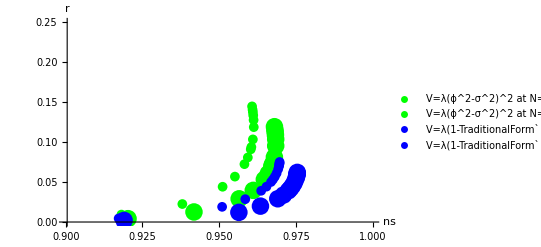

```mathematica
ns60Listμ
r60Listμ
nsmin = 0.9; nsmax = 1; rmin = 0; rmax = 0.25;
p3 = ListPlot[Legended[Transpose[{ns60Listμ,r60Listμ}],"V=λ(1-TraditionalForm` ) at N=60"],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotMarkers->{●,18},PlotStyle->Blue];
p4 = ListPlot[Legended[Transpose[{ns50Listμ,r50Listμ}],"V=λ(1-TraditionalForm` ) at N=60"],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotMarkers->{●,10},PlotStyle->Blue,PlotLegends->PointLegend[Automatic,{"Hilltop at N=50"}]];
Show[p1,p2,p3,p4]
```

### Hilltop Models: V=λ(1 - (ϕ/μ)^2 )

```mathematica
μ4List = {5,7,10,12,15,17,20,22,25,30,40,50,60,70,80,100};
ns60Listμ4={};ns50Listμ4={};r60Listμ4={};r50Listμ4={};
Do[
Print["μ = ",μ];
v[x_]:=(0.01)*(1-(x/μ)^4);
vp[x_]=v'[x];
vpp[x_] = v''[x];

ni = 60; (* initial value f n for integration *)
nf = -1.8; (* final value of n for integration *)
ni2 = 60;
nf2 = 0;
n1guess = -1;

ϕsol2=findϕsol[v,vp,vpp,ni,nf,ni2,nf2,n1guess,False,False, True];
{ns,r,ϵ2} = findNsR[v,vp,ϕsol2,ni2,nf2,False,False]; 
AppendTo[ns60Listμ4,ns/.{n->60}];
AppendTo[ns50Listμ4,ns/.{n->50}];
AppendTo[r60Listμ4,r/.{n->60}];
AppendTo[r50Listμ4,r/.{n->50}];
,{μ,μ4List}]
```

μ = 5

ϕ0list = {-5.88887,-4.41822,-0.67889-4.85393 ⅈ,-0.67889+4.85393 ⅈ,0.67889-4.85393 ⅈ,0.67889+4.85393 ⅈ,4.41822,5.88887}

Greater::nord: Invalid comparison with -0.67889 - 4.85393\ ⅈ attempted.

Greater::nord: Invalid comparison with -0.67889 + 4.85393\ ⅈ attempted.

Greater::nord: Invalid comparison with 0.67889  - 4.85393\ ⅈ attempted.

General::stop: Further output of Greater :: nord will be suppressed during this calculation.

ϕi1s = {1.08556}

InterpolatingFunction::dmval: Input value {-4.2293} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-2.46402} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-2.10549} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

μ = 7

ϕ0list = {-7.83,-6.38694,-0.692685-6.89426 ⅈ,-0.692685+6.89426 ⅈ,0.692685-6.89426 ⅈ,0.692685+6.89426 ⅈ,6.38694,7.83}

ϕi1s = {2.04259}

μ = 10

ϕ0list = {-10.7896,-9.36129,-0.700037-9.92547 ⅈ,-0.700037+9.92547 ⅈ,0.700037-9.92547 ⅈ,0.700037+9.92547 ⅈ,9.36129,10.7896}

ϕi1s = {3.87275}

NDSolve::ndsz: At n == -1.75189, step size is effectively zero; singularity or stiff system suspected.

Power::infy: Infinite expression 1/0. encountered.

FindRoot::nlnum: The function value {ComplexInfinity} is not a list of numbers with dimensions {1} at {n} = {-2.16867}.

μ = 12

ϕ0list = {-12.7748,-11.3508,-0.702197-11.9378 ⅈ,-0.702197+11.9378 ⅈ,0.702197-11.9378 ⅈ,0.702197+11.9378 ⅈ,11.3508,12.7748}

ϕi1s = {5.28701}

NDSolve::ndsz: At n == -1.69395, step size is effectively zero; singularity or stiff system suspected.

Power::infy: Infinite expression 1/0. encountered.

FindRoot::nlnum: The function value {ComplexInfinity} is not a list of numbers with dimensions {1} at {n} = {-1.89407}.

μ = 15

ϕ0list = {-15.7604,-14.3399,-0.703964-14.9501 ⅈ,-0.703964+14.9501 ⅈ,0.703964-14.9501 ⅈ,0.703964+14.9501 ⅈ,14.3399,15.7604}

ϕi1s = {7.6112}

NDSolve::ndsz: At n == -1.63249, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve :: ndsz will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

FindRoot::nlnum: The function value {ComplexInfinity} is not a list of numbers with dimensions {1} at {n} = {-1.64917}.

General::stop: Further output of FindRoot :: nlnum will be suppressed during this calculation.

μ = 17

ϕ0list = {-17.7538,-16.3347,-0.70466-16.956 ⅈ,-0.70466+16.956 ⅈ,0.70466-16.956 ⅈ,0.70466+16.956 ⅈ,16.3347,17.7538}

ϕi1s = {9.25967}

μ = 20

ϕ0list = {-20.7464,-19.3287,-0.705339-19.9626 ⅈ,-0.705339+19.9626 ⅈ,0.705339-19.9626 ⅈ,0.705339+19.9626 ⅈ,19.3287,20.7464}

ϕi1s = {11.838}

μ = 22

ϕ0list = {-22.7427,-21.3256,-0.705646-21.966 ⅈ,-0.705646+21.966 ⅈ,0.705646-21.966 ⅈ,0.705646+21.966 ⅈ,21.3256,22.7427}

ϕi1s = {13.6101}

μ = 25

ϕ0list = {-25.7383,-24.3218,-0.705975-24.97 ⅈ,-0.705975+24.97 ⅈ,0.705975-24.97 ⅈ,0.705975+24.97 ⅈ,24.3218,25.7383}

ϕi1s = {16.3273}

μ = 30

ϕ0list = {-30.7329,-29.3171,-0.706321-29.975 ⅈ,-0.706321+29.975 ⅈ,0.706321-29.975 ⅈ,0.706321+29.975 ⅈ,29.3171,30.7329}

ϕi1s = {20.9687}

μ = 40

ϕ0list = {-40.7263,-39.3112,-0.706665-39.9813 ⅈ,-0.706665+39.9813 ⅈ,0.706665-39.9813 ⅈ,0.706665+39.9813 ⅈ,39.3112,40.7263}

ϕi1s = {30.5022}

μ = 50

ϕ0list = {-50.7224,-49.3076,-0.706824-49.985 ⅈ,-0.706824+49.985 ⅈ,0.706824-49.985 ⅈ,0.706824+49.985 ⅈ,49.3076,50.7224}

ϕi1s = {40.2141}

μ = 60

ϕ0list = {-60.7198,-59.3052,-0.70691-59.9875 ⅈ,-0.70691+59.9875 ⅈ,0.70691-59.9875 ⅈ,0.70691+59.9875 ⅈ,59.3052,60.7198}

ϕi1s = {50.0191}

μ = 70

ϕ0list = {-70.718,-69.3035,-0.706962-69.9893 ⅈ,-0.706962+69.9893 ⅈ,0.706962-69.9893 ⅈ,0.706962+69.9893 ⅈ,69.3035,70.718}

ϕi1s = {59.8786}

μ = 80

ϕ0list = {-80.7166,-79.3022,-0.706996-79.9906 ⅈ,-0.706996+79.9906 ⅈ,0.706996-79.9906 ⅈ,0.706996+79.9906 ⅈ,79.3022,80.7166}

ϕi1s = {69.7727}

μ = 100

ϕ0list = {-100.715,-99.3003,-0.707036-99.9925 ⅈ,-0.707036+99.9925 ⅈ,0.707036-99.9925 ⅈ,0.707036+99.9925 ⅈ,99.3003,100.715}

ϕi1s = {89.6237}

{0.954032,0.957231,0.96317,0.965313,0.967817,0.968124,0.969725,0.970543,0.971498,0.972597,0.973804,0.974406,0.974745,0.974954,0.975091,0.975254}

{0.000574391,0.00172612,0.00463853,0.00719292,0.0113856,0.0143184,0.0183551,0.0208577,0.0242952,0.0292091,0.0365661,0.0416694,0.0453652,0.0481483,0.0503129,0.0534529}

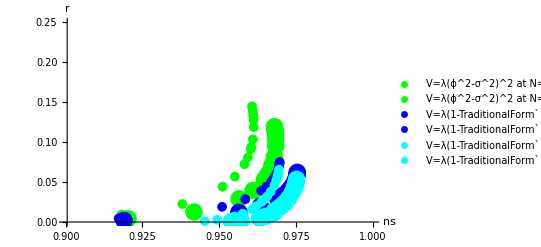

```mathematica
ns60Listμ4
r60Listμ4
nsmin = 0.9; nsmax = 1; rmin = 0; rmax = 0.25;
p5 = ListPlot[Legended[Transpose[{ns60Listμ4,r60Listμ4}],"V=λ(1-TraditionalForm` ) at N=60"],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotMarkers->{●,18},PlotStyle->Cyan];
p6 = ListPlot[Legended[Transpose[{ns50Listμ4,r50Listμ4}],"V=λ(1-TraditionalForm` ) at N=60"],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotMarkers->{●,10},PlotStyle->Cyan,PlotLegends->PointLegend[Automatic,{"Hilltop at N=50"}]];
Show[p1,p2,p3,p4,p5,p6]
```

### Natural Inflation Models: V=λ(1 + Cos(ϕ/ff) )

```mathematica
fList = {3};(*{5,7,10,12,15,17,20,22,25};*)
ns60Listf={};ns50Listf={};r60Listf={};r50Listf={};
Do[
v[x_]:= 0.5*(0.01)*(1+Cos[x/ff]);
vp[x_]=v'[x];
vpp[x_] = v''[x];

ni = 60; (* initial value f n for integration *)
nf = -1.8; (* final value of n for integration *)
ni2 = 60;
nf2 = 0;
n1guess = -1;

ϕsol2=findϕsol[v,vp,vpp,ni,nf,ni2,nf2,n1guess,True,True, True];
{ns,r,ϵ2} = findNsR[v,vp,ϕsol2,ni2,nf2,True,True]; 
AppendTo[ns60Listf,ns/.{n->60}];
AppendTo[ns50Listf,ns/.{n->50}];
AppendTo[r60Listf,r/.{n->60}];
AppendTo[r50Listf,r/.{n->50}];
,{ff,fList}]
```

```mathematica
ns50Listf
r50Listf
nsmin = 0.9; nsmax = 1; rmin = 0; rmax = 0.2;
p5 = ListPlot[Transpose[{ns60Listf,r60Listf}],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotMarkers->{●,20},PlotStyle->Purple,PlotLegends->PointLegend[Automatic,{"Hilltop at N=60"}]];
p6 = ListPlot[Transpose[{ns50Listf,r50Listf}],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotMarkers->{●,12},PlotStyle->Purple,PlotLegends->PointLegend[Automatic,{"Hilltop at N=50"}]];

(* Show[p1,p2,p3,p4,p5,p6] *)
Show[p5,p6]
```

### Starobinsky’s R^2 Model: V(ϕ)=M_pl^2/(4α)(1-exp[-√(2/3)ϕ/M_pl])^2

```mathematica
v[x_]:=(0.1)*(1-Exp[-√(2/3)*x])^2;
vp[x_]=v'[x];
vpp[x_] = v''[x];

ni = 60; (* initial value f n for integration *)
nf = -1.8; (* final value of n for integration *)
ni2 = 60;
nf2 = 0;
n1guess = -1;

ϕsol2=findϕsol[v,vp,vpp,ni,nf,ni2,nf2,n1guess,False,False, False];
{ns,r,ϵ2} = findNsR[v,vp,ϕsol2,ni2,nf2,False,False];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

ϕ0list = {0.,0.940178}

vacuumArray = {0.}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve :: ratnz will be suppressed during this calculation.

ϕi1s = {5.45315}

InterpolatingFunction::dmval: Input value {-2.34373} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-1.95601} lies outside the range of data in the interpolating function. Extrapolation will be used.

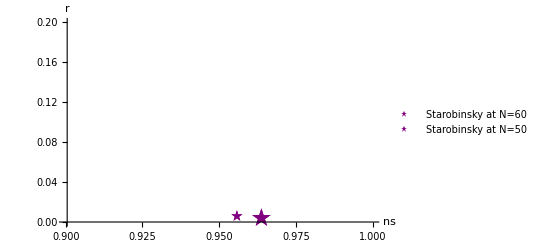

```mathematica
nsmin = 0.9; nsmax = 1; rmin = 0; rmax = 0.2;
p7 = ListPlot[Legended[Thread[{{ns/.{n->60}},{r/.{n->60}}}],"Starobinsky at N=60"],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotMarkers->{★,20},PlotStyle->Purple];
p8 = ListPlot[Legended[Thread[{{ns/.{n->50}},{r/.{n->50}}}],"Starobinsky at N=50"],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotMarkers->{★,12},PlotStyle->Purple];

(* Show[p1,p2,p3,p4,p5,p6] *)
Show[p7,p8]
```

### Shaposhnikov model: V(ϕ)=λM_pl^2/(4 ξ^2)(1+exp[(-2ϕ)/(√6 M_pl)])^-2

```mathematica
v[x_]:=(0.1)*(1+Exp[-2*x/√6])^-2;
vp[x_]=v'[x];
vpp[x_] = v''[x];

ni = 60; (* initial value f n for integration *)
nf = -1.8; (* final value of n for integration *)
ni2 = 60;
nf2 = 0;
n1guess = -1;

ϕsol2=findϕsol[v,vp,vpp,ni,nf,ni2,nf2,n1guess,False,False, False];
{ns,r,ϵ2} = findNsR[v,vp,ϕsol2,ni2,nf2,False,False];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

ϕ0list = {-2.2857}

vacuumArray = {}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

ϕi1s = {5.27113}

InterpolatingFunction::dmval: Input value {-1.81269} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-1.87451} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-1.87534} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

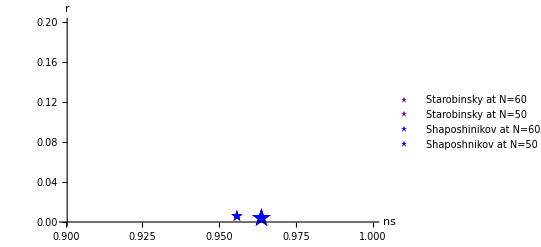

```mathematica
nsmin = 0.9; nsmax = 1; rmin = 0; rmax = 0.2;
p9 = ListPlot[Legended[Thread[{{ns/.{n->60}},{r/.{n->60}}}],"Shaposhinikov at N=60"],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotMarkers->{★,20},PlotStyle->Blue];
p10 = ListPlot[Legended[Thread[{{ns/.{n->50}},{r/.{n->50}}}],"Shaposhnikov at N=50"],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotMarkers->{★,12},PlotStyle->Blue];
Show[p7,p8,p9,p10]
```

### D-brane inflation: V(ϕ)=λ^4(1-(m/ϕ)^p)

m = 1

jj = 1

ϕ0list = {-0.478318,1.47832}

vacuumArray = {}

ϕi1s = {6.19259}

NDSolve::ndsz: At n == -1.48307, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {-1.65263} lies outside the range of data in the interpolating function. Extrapolation will be used.

Power::infy: Infinite expression 1/0. encountered.

FindRoot::nlnum: The function value {ComplexInfinity} is not a list of numbers with dimensions {1} at {n} = {-1.65263}.

m = 10

jj = 1

ϕ0list = {-0.663132,0.765743,9.23426,10.6631}

vacuumArray = {0.765743,9.23426}

ϕi1s = {18.7296}

NDSolve::ndsz: At n == -1.5258, step size is effectively zero; singularity or stiff system suspected.

m = 20

jj = 1

ϕ0list = {-0.683732,0.734048,19.266,20.6837}

vacuumArray = {0.734048,19.266}

ϕi1s = {29.5603}

NDSolve::ndsz: At n == -1.47606, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve :: ndsz will be suppressed during this calculation.

m = 40

jj = 1

ϕ0list = {-0.69503,0.720069,39.2799,40.695}

vacuumArray = {0.720069,39.2799}

ϕi1s = {50.1524}

m = 60

jj = 1

ϕ0list = {-0.698964,0.715643,59.2844,60.699}

vacuumArray = {0.715643,59.2844}

ϕi1s = {70.3938}

m = 80

jj = 1

ϕ0list = {-0.700965,0.71347,79.2865,80.701}

vacuumArray = {0.71347,79.2865}

ϕi1s = {90.5256}

m = 100

jj = 1

ϕ0list = {-0.702176,0.712179,99.2878,100.702}

vacuumArray = {0.712179,99.2878}

ϕi1s = {110.609}

m = 1

jj = 2

ϕ0list = {-1.41421,1.41421}

vacuumArray = {}

ϕi1s = {4.78871}

InterpolatingFunction::dmval: Input value {-2.34438} lies outside the range of data in the interpolating function. Extrapolation will be used.

Power::infy: Infinite expression 1/0. encountered.

FindRoot::nlnum: The function value {ComplexInfinity} is not a list of numbers with dimensions {1} at {n} = {-2.34438}.

m = 10

jj = 2

ϕ0list = {-10.6436,-9.19929,-1.44434,1.44434,9.19929,10.6436}

vacuumArray = {1.44434,9.19929}

ϕi1s = {17.8781}

m = 20

jj = 2

ϕ0list = {-20.6728,-19.2514,-1.42139,1.42139,19.2514,20.6728}

vacuumArray = {1.42139,19.2514}

ϕi1s = {28.9683}

m = 40

jj = 2

ϕ0list = {-40.6892,-39.2732,-1.41599,1.41599,39.2732,40.6892}

vacuumArray = {1.41599,39.2732}

ϕi1s = {49.782}

m = 60

jj = 2

ϕ0list = {-60.695,-59.28,-1.415,1.415,59.28,60.695}

vacuumArray = {1.415,59.28}

ϕi1s = {70.1237}

m = 80

jj = 2

ϕ0list = {-80.6979,-79.2833,-1.41466,1.41466,79.2833,80.6979}

vacuumArray = {1.41466,79.2833}

ϕi1s = {90.3129}

m = 100

jj = 2

ϕ0list = {-100.7,-99.2852,-1.4145,1.4145,99.2852,100.7}

vacuumArray = {1.4145,99.2852}

ϕi1s = {110.433}

m = 1

jj = 3

ϕ0list = {-1.02359,1.3666}

vacuumArray = {}

ϕi1s = {3.93105}

InterpolatingFunction::dmval: Input value {-3.31012} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

FindRoot::nlnum: The function value {ComplexInfinity} is not a list of numbers with dimensions {1} at {n} = {-3.31012}.

General::stop: Further output of FindRoot :: nlnum will be suppressed during this calculation.

m = 10

jj = 3

ϕ0list = {-2.10181,2.14239,9.15929,10.6255}

vacuumArray = {2.14239,9.15929}

ϕi1s = {17.1685}

m = 20

jj = 3

ϕ0list = {-2.1188,2.12386,19.236,20.6623}

vacuumArray = {2.12386,19.236}

ϕi1s = {28.4419}

m = 40

jj = 3

ϕ0list = {-2.121,2.12164,39.2663,40.6835}

vacuumArray = {2.12164,39.2663}

ϕi1s = {49.4368}

m = 60

jj = 3

ϕ0list = {-2.12123,2.12141,59.2755,60.6911}

vacuumArray = {2.12141,59.2755}

ϕi1s = {69.8669}

m = 80

jj = 3

ϕ0list = {-2.12128,2.12136,79.28,80.695}

vacuumArray = {2.12136,79.28}

ϕi1s = {90.1085}

m = 100

jj = 3

ϕ0list = {-2.1213,2.12134,99.2827,100.697}

vacuumArray = {2.12134,99.2827}

ϕi1s = {110.263}

m = 1

jj = 4

ϕ0list = {-1.32978,1.32978}

vacuumArray = {}

ϕi1s = {3.37366}

m = 10

jj = 4

ϕ0list = {-10.6087,-9.11282,-2.84714,2.84714,9.11282,10.6087}

vacuumArray = {2.84714,9.11282}

ϕi1s = {16.5731}

m = 20

jj = 4

ϕ0list = {-20.6522,-19.2197,-2.82956,2.82956,19.2197,20.6522}

vacuumArray = {2.82956,19.2197}

ϕi1s = {27.9727}

m = 40

jj = 4

ϕ0list = {-40.6779,-39.2592,-2.8285,2.8285,39.2592,40.6779}

vacuumArray = {2.8285,39.2592}

ϕi1s = {49.1147}

m = 60

jj = 4

ϕ0list = {-60.6872,-59.271,-2.82844,2.82844,59.271,60.6872}

vacuumArray = {2.82844,59.271}

ϕi1s = {69.6227}

m = 80

jj = 4

ϕ0list = {-80.692,-79.2767,-2.82843,2.82843,79.2767,80.692}

vacuumArray = {2.82843,79.2767}

ϕi1s = {89.912}

m = 100

jj = 4

ϕ0list = {-100.695,-99.28,-2.82843,2.82843,99.28,100.695}

vacuumArray = {2.82843,99.28}

ϕi1s = {110.099}

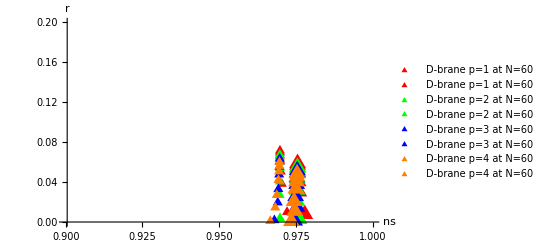

```mathematica
mList = {1,10,20,40,60,80,100};
pList={1,2,3,4};
colorList = {Red,Green,Blue,Orange}; jj=1;
nsmin = 0.9; nsmax = 1; rmin = 0; rmax = 0.2; p11={};p12={};
Do[ns60Listm={};ns50Listm={};r60Listm={};r50Listm={};
Do[
Print["m = ",m];
Print["jj = ",jj];
v[x_]:=(0.01)*(1-(m/x)^p);
vp[x_]=v'[x];
vpp[x_] = v''[x];

ni = 60; (* initial value f n for integration *)
nf = -1.8; (* final value of n for integration *)
ni2 = 60;
nf2 = 0;
n1guess = -1;

ϕsol2=findϕsol[v,vp,vpp,ni,nf,ni2,nf2,n1guess,False,False, False];
{ns,r,ϵ2} = findNsR[v,vp,ϕsol2,ni2,nf2,False,False]; 
AppendTo[ns60Listm,ns/.{n->60}];
AppendTo[ns50Listm,ns/.{n->50}];
AppendTo[r60Listm,r/.{n->60}];
AppendTo[r50Listm,r/.{n->50}];
,{m,mList}]
AppendTo[p11, ListPlot[Legended[Transpose[{ns60Listm,r60Listm}],StringJoin["D-brane p=",ToString[p]," at N=60"]],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotMarkers->{▲,20},PlotStyle->colorList[[jj]]]];
AppendTo[p11 , ListPlot[Legended[Transpose[{ns50Listm,r50Listm}],StringJoin["D-brane p=",ToString[p]," at N=60"]],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotMarkers->{▲,12},PlotStyle->colorList[[jj]]]];
jj = jj+1;
,{p,pList}];

Show[p11]
```

### Exponential potential: V(ϕ)=λ^4(1-exp[-qϕ/M_pl])

```mathematica
qList = {0.01,0.05,0.1,0.5,1};
ns60Listq={};ns50Listq={};r60Listq={};r50Listq={};
Do[
v[x_]:=(0.01)*(1-Exp[-q*x]);
vp[x_]=v'[x];
vpp[x_] = v''[x];

ni = 60; (* initial value f n for integration *)
nf = -1.8; (* final value of n for integration *)
ni2 = 60;
nf2 = 0;
n1guess = -1;

ϕsol2=findϕsol[v,vp,vpp,ni,nf,ni2,nf2,n1guess,False,False, True];
{ns,r,ϵ2} = findNsR[v,vp,ϕsol2,ni2,nf2,False,False]; 
AppendTo[ns60Listq,ns/.{n->60}];
AppendTo[ns50Listq,ns/.{n->50}];
AppendTo[r60Listq,r/.{n->60}];
AppendTo[r50Listq,r/.{n->50}];
,{q,qList}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

ϕ0list = {-0.709619,0.704619}

vacuumArray = {}

ϕi1s = t

Last::normal: Nonatomic expression expected at position 1 in Last[t].

NDSolve::ndinnt: Initial condition Last[t] is not a number or a rectangular array of numbers.

ReplaceAll::reps: {All} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

FindRoot::nlnum: The function value -1. is not a list of numbers with dimensions {1} at {n} = {-1.}.

NDSolve::overdet: There are fewer dependent variables, {ϕ[n]}, than equations, so the system is overdetermined.

General::ivar: 60 is not a valid variable.

General::ivar: 50 is not a valid variable.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve :: ratnz will be suppressed during this calculation.

ϕ0list = {-0.719909,0.694894}

vacuumArray = {}

ϕi1s = t

Last::normal: Nonatomic expression expected at position 1 in Last[t].

NDSolve::ndinnt: Initial condition Last[t] is not a number or a rectangular array of numbers.

FindRoot::nlnum: The function value -1. is not a list of numbers with dimensions {1} at {n} = {-1.}.

NDSolve::overdet: There are fewer dependent variables, {ϕ[n]}, than equations, so the system is overdetermined.

General::ivar: 60 is not a valid variable.

General::stop: Further output of General :: ivar will be suppressed during this calculation.

ϕ0list = {-0.733352,0.683226}

vacuumArray = {}

ϕi1s = t

Last::normal: Nonatomic expression expected at position 1 in Last[t].

General::stop: Further output of Last :: normal will be suppressed during this calculation.

NDSolve::ndinnt: Initial condition Last[t] is not a number or a rectangular array of numbers.

General::stop: Further output of NDSolve :: ndinnt will be suppressed during this calculation.

FindRoot::nlnum: The function value -1. is not a list of numbers with dimensions {1} at {n} = {-1.}.

General::stop: Further output of FindRoot :: nlnum will be suppressed during this calculation.

NDSolve::overdet: There are fewer dependent variables, {ϕ[n]}, than equations, so the system is overdetermined.

General::stop: Further output of NDSolve :: overdet will be suppressed during this calculation.

ϕ0list = {-0.872529,0.605467}

vacuumArray = {}

ϕi1s = t

ϕ0list = {-1.22795,0.5348}

vacuumArray = {}

ϕi1s = t

```mathematica
nsmin = 0.9; nsmax = 1; rmin = 0; rmax = 0.2;
p12 = ListPlot[Legended[Transpose[{ns60Listq,r60Listq}],"Exponential at N=60"],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotMarkers->{●,20},PlotStyle->Purple];
p13 = ListPlot[Legended[Transpose[{ns50Listq,r50Listq}],"Exponential at N=50"],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotMarkers->{●,12},PlotStyle->Purple];

(* Show[p1,p2,p3,p4,p5,p6] *)
Show[p12,p13]
```

ReplaceAll::reps: {All} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::ivar: 60. is not a valid variable.

ReplaceAll::reps: {All} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

General::ivar: 60. is not a valid variable.

General::stop: Further output of General :: ivar will be suppressed during this calculation.

ReplaceAll::reps: {All} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::ivar: 50. is not a valid variable.

ReplaceAll::reps: {All} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

General::ivar: 50. is not a valid variable.

General::stop: Further output of General :: ivar will be suppressed during this calculation.

-Graphics-

## Find Zeros

```mathematica
{ϵsr,ηsr,ηsrL} = findSRparams[v,vp,vpp,ϕsol2,ni2,nf2,True,True];
Plot[{Legended[Evaluate[ηsr[n]],"ηsr"],Legended[Evaluate[ηsrL[n]],"ηsrL"]},{n,nf2,ni2},AxesLabel->{N,"ηsr"},PlotRange->{{nf2,ni2},{0,3}}]
(* Plots,Prints *)
Print["ns[60] = ",ns/.{n->60}," and r[60] = ",r/.{n->60}];
Print["ns[50] = ",ns/.{n->50}," and r[50] = ",r/.{n->50}];
```

```mathematica
Zη = countAllZeros[v,vpp,ηsr,nf2,ni2,0.1,5];
Print["Zη = ",Zη];
```

```mathematica
Zϵ = findZϵ[ϕsol,nf2,ni2,0.1,5];
Print["Zϵ = ",Zϵ];
```

```mathematica
Zη = findZη[ϕsol,nf2,ni2,0.1,5];
Print["Zη = ",Zη];
```

```mathematica
MaxValue[ϵsr[n],n]
Plot[Evaluate[ϵsr[n]],{n,0,80},AxesLabel->{N,"ϵsr"},PlotRange->{0,2}]
f1[n_]=D[ϵsr[n],{n,1}];
Plot[Evaluate[f1[n]],{n,0,80},AxesLabel->{N,"ϵsr1"},PlotRange->{-1,1}]
f2[n_]=D[ϵsr[n],{n,2}];
MaxValue[f2[n],n]
Plot[Evaluate[f2[n]],{n,0,80},AxesLabel->{N,"ϵsr2"},PlotRange->{-1,1}]
```

```mathematica
Plot[Evaluate[ηsr[n]],{n,0,80},AxesLabel->{N,"ηsr1"}]
f1[n_]=D[ηsr[n],{n,1}];
Plot[Evaluate[f1[n]],{n,0,80},AxesLabel->{N,"ηsr1"}]
f2[n_]=D[ηsr[n],{n,2}];
Plot[Evaluate[f2[n]],{n,0,80},AxesLabel->{N,"ηsr2"}]
```

## Monomial Loop for Planck Plot

ϕ0list = {-1.41421,0.,1.41421}

vacuumArray = {0.}

ϕi1s = {15.5563}

ϕ0list = {-0.471405,0.471405}

vacuumArray = {}

ϕi1s = {8.95669}

NDSolve::ndsz: At n == -1.61846, step size is effectively zero; singularity or stiff system suspected.

ϕ0list = {-0.707107,0.707107}

vacuumArray = {}

ϕi1s = {10.9772}

NDSolve::ndsz: At n == -1.39548, step size is effectively zero; singularity or stiff system suspected.

ϕ0list = {-2.12132,0.,2.12132}

vacuumArray = {0.}

ϕi1s = {19.0919}

ϕ0list = {-2.82843,0.,2.82843}

vacuumArray = {0.}

ϕi1s = {22.0907}

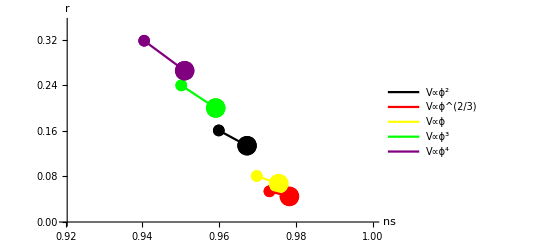

```mathematica
(* Loop over several monomial potentials and generate and ns vs r plot *)
ni = 60; nf = -1.8; ni2 = 60; nf2 = 0; n1guess = -1;
pList = {2,2/3,1,3,4};plotList = {}; 
clrList = {Black,Red,Yellow,Green,Purple}; ii=1;
nsmin = 0.92; nsmax = 1; rmin = 0; rmax = 0.35;
Do[
Clear[v,vp,vpp,ns,r,ϵ2];
v[x_] := x^p;
vp[x_]=v'[x];
vpp[x_] = v''[x];
ϕsol2=findϕsol[v,vp,vpp,ni,nf,ni2,nf2,n1guess,False,False,False];
{ns,r,ϵ2} = findNsR[v,vp,ϕsol2,ni2,nf2,False,False]; 
AppendTo[plotList,ListPlot[Thread[{{ns/.{n->50}},{r/.{n->50}}}],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotMarkers->{●,12},PlotStyle->clrList[[ii]],PlotLegends->PointLegend[Automatic,{"N=50"},LegendFunction->"Frame"]]];
AppendTo[plotList,ListPlot[Thread[{{ns/.{n->60}},{r/.{n->60}}}],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotMarkers->{●,20},PlotStyle->clrList[[ii]],PlotLegends->PointLegend[Automatic,"N=60",LegendFunction->"Frame"]]];
AppendTo[plotList,ListLinePlot[Legended[{{ns/.{n->50},r/.{n->50}},{ns/.{n->60},r/.{n->60}}},V∝ϕ^pList[[ii]]],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotStyle->clrList[[ii]]]];
ii = ii+1,{p,pList}]
Show[plotList]
```